# Final Exam Review

## Sequences and Series

```mathematica
SumConvergence[n!/Exp[n^2],n]
```

True

```mathematica
SumConvergence[2^n/(3^n-Exp[-n]),n]
```

True

```mathematica
Limit[(3n/(3n+3))^n,n->Infinity]
```

1/ⅇ

```mathematica
Apart[(3n/(3n+3))]
```

1-1/(1+n)

## Taylor Series

```mathematica
Series[x*Sin[x^2],{x,0,4}]
```

x^3+O[x]^5

```mathematica
Series[x*Sin[x^2],{x,0,19}]
```

x^3-x^7/6+x^11/120-x^15/5040+x^19/362880+O[x]^20

```mathematica
Series[Exp[-x]Sin[x],{x,Pi/2,3}]
```

ⅇ^(-π/2)-ⅇ^(-π/2) (x-π/2)+1/3 ⅇ^(-π/2) (x-π/2)^3+O[x-π/2]^4

```mathematica
Limit[(Log[x+1]+Sin[3x])^2/(Tan[3x]*Tan[x]),x->0]
```

16/3

#### Final Exam question

```mathematica
Series[1/(1-x^3),{x,0,12}]
```

1+x^3+x^6+x^9+x^12+O[x]^13

```mathematica
Series[x/(1-x^3),{x,0,12}]
```

x+x^4+x^7+x^10+O[x]^13

```mathematica
Integrate[Series[x/(1-x^3),{x,0,12}],x]
```

x^2/2+x^5/5+x^8/8+x^11/11+O[x]^14

## Parametric Equations

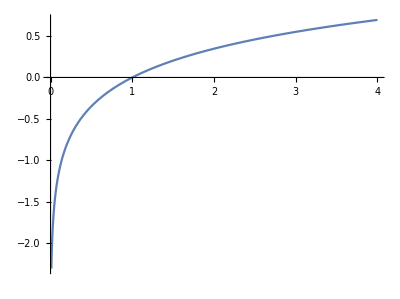

```mathematica
ParametricPlot[{t^2,Log[t]},{t,1/10,2}]
```

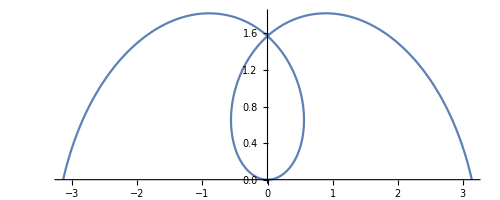

```mathematica
ParametricPlot[{t*Cos[t],t*Sin[t]},{t,-Pi,Pi}]
```

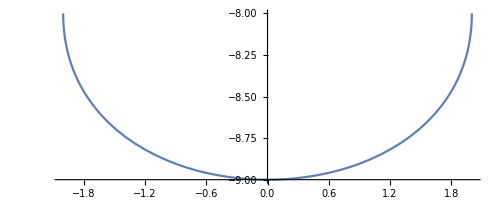

```mathematica
ParametricPlot[{t^3-3t,t^2-9},{t,-1,1}]
```

```mathematica
Integrate[Sqrt[(2t-3)^2+(5t^4)^2],{t,1,4}]
```

∫_1^4 √(25 t^8+(-3+2 t)^2)ⅆt

```mathematica
Simplify[∫_1^4 √(25 t^8+(-3+2 t)^2)ⅆt]
```

∫_1^4 √((3-2 t)^2+25 t^8)ⅆt

```mathematica
NIntegrate[√((3-2 t)^2+25 t^8),{t,1,4}]
```

1023.03

```mathematica
NumberForm[1023.0327637173964,16]
```

1023.032763717396

```mathematica
Integrate[Sqrt[(1-2Cos[t])^2+(2Sin[t])^2],{t,0,7Pi}]
```

14 EllipticE[-8]

```mathematica
N[14 EllipticE[-8]]
```

46.7771

```mathematica
Integrate[Sqrt[(18t)^2+(18t^2)^2],{t,0,3}]
```

-6+60 √10

## Polar Coordinates

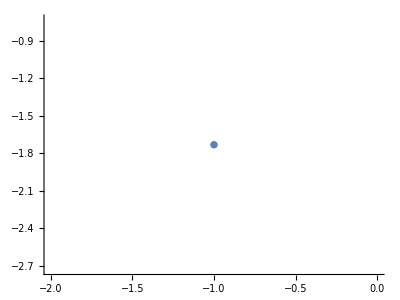

```mathematica
ListPolarPlot[Table[{n(-2Pi)/3,2n},{n,1}],AspectRatio->Automatic]
```

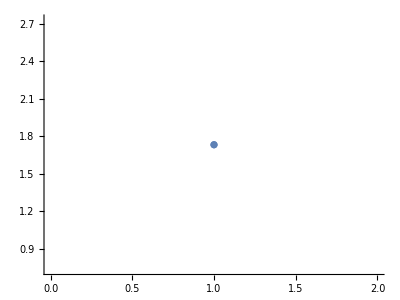

```mathematica
ListPolarPlot[Table[{n(Pi)/3,2n},{n,1}],AspectRatio->Automatic]
```

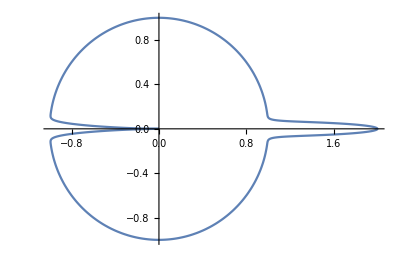

```mathematica
PolarPlot[r=1+Cos[t]^999,{t,-Pi,Pi}]
```

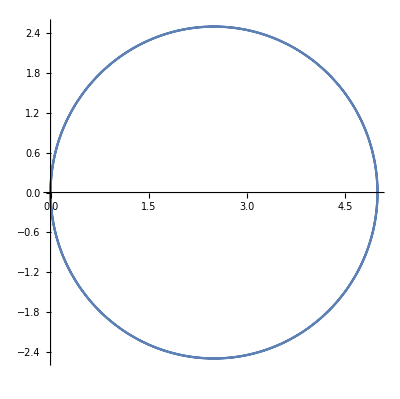

```mathematica
PolarPlot[r=5Cos[t],{t,0,2Pi}]
```

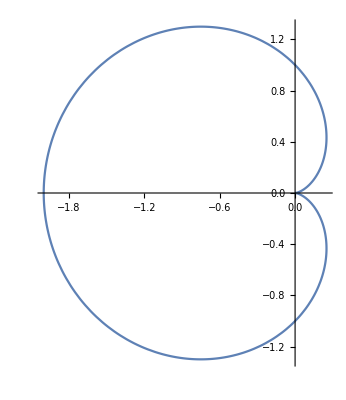

```mathematica
PolarPlot[r=1-Cos[t],{t,0,2Pi}]
```

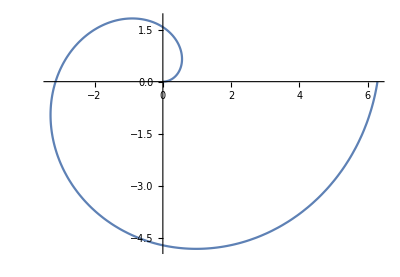

```mathematica
PolarPlot[r=t,{t,0,2Pi}]
```

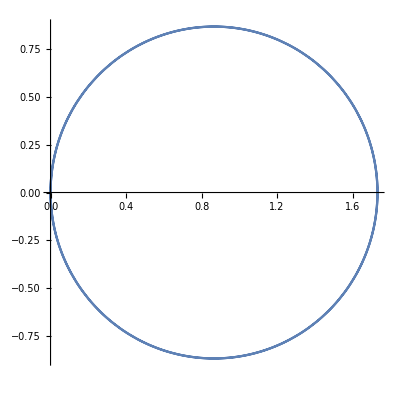

```mathematica
PolarPlot[Sqrt[3]*Cos[t],{t,0,2Pi}]
```

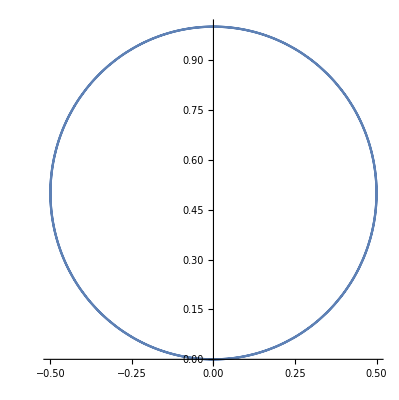

```mathematica
PolarPlot[Sin[t],{t,0,2Pi}]
```

## Conic Sections

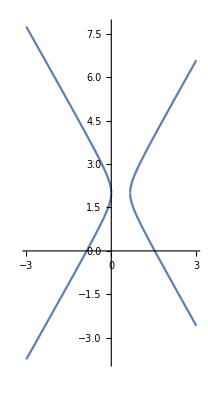

```mathematica
Plot[y/.Solve[(x-1)^2+(y-2)^2==(2x-1)^2],{x,-3,3},AspectRatio->Automatic]
```

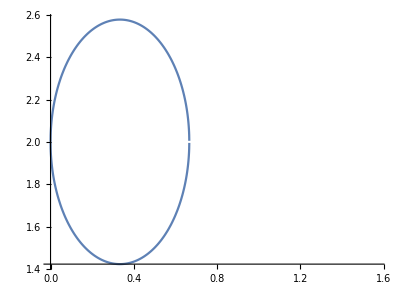

```mathematica
Plot[y/.Solve[(2x-1)^2+(y-2)^2==(x-1)^2],{x,0,Pi/2},AspectRatio->Automatic]
```

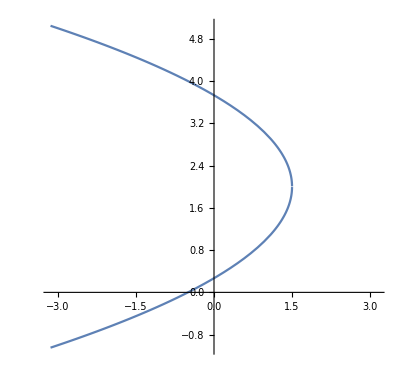

```mathematica
Plot[y/.Solve[(x-1)^2+(y-2)^2==(x-2)^2],{x,-Pi,Pi},AspectRatio->Automatic]
```

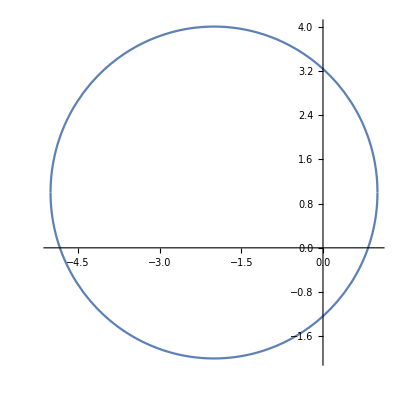

```mathematica
Plot[y/.Solve[y^2-2y+3==7-4x-x^2],{x,-5,1},AspectRatio->Automatic]
```

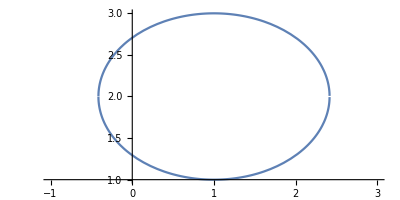

```mathematica
Plot[y/.Solve[x^2-2x+2y^2-8y+7==0],{x,-1,3},AspectRatio->Automatic]
```

## Integration

```mathematica
Integrate[ArcCos[x],x]
```

-√(1-x^2)+x ArcCos[x]

```mathematica
Integrate[(Sin[x])^5,x]
```

-(5 Cos[x])/8+5/48 Cos[3 x]-1/80 Cos[5 x]

```mathematica
Integrate[Sqrt[x]*Log[x],x]
```

2/9 x^(3/2) (-2+3 Log[x])

```mathematica
Integrate[x*Sec[x]^2,x]
```

Log[Cos[x]]+x Tan[x]

```mathematica
Integrate[ArcTan[x],x]
```

x ArcTan[x]-1/2 Log[1+x^2]

```mathematica
Integrate[Sin[x]^4*Cos[x]^3,{x,0,Pi/2}]
```

2/35

```mathematica
Integrate[Tan[x]^2*Sec[x]^4,x]
```

-(2 Tan[x])/15-1/15 Sec[x]^2 Tan[x]+1/5 Sec[x]^4 Tan[x]

```mathematica
Integrate[7*Sin[x]^2*Cos[x]^3,x]
```

7 (Sin[x]/8-1/48 Sin[3 x]-1/80 Sin[5 x])

## Average Value of an Integral

```mathematica
Integrate[Cos[x]^2,{x,0,Pi}]
```

π/2

## Solids of Revolution

```mathematica
Integrate[Pi*(3y-y^(3/2)),{y,0,9}]
```

(243 π)/10

#### Area between y=x^2 and y=2x rotated about y axis

```mathematica
Integrate[2Pi*(2x^2-x^3),{x,0,2}]
```

(8 π)/3

```mathematica
Integrate[Pi*((Sqrt[y])^2-(y/2)^2),{y,0,4}]
```

(8 π)/3

#### Area between y=x^2 and y=2x rotated about x=3

```mathematica
Integrate[2Pi*(3-x)(2x-x^2),{x,0,2}]
```

(16 π)/3

```mathematica
Integrate[Pi*((3-(y/2))^2-(3-Sqrt[y])^2),{y,0,4}]
```

(16 π)/3

## Limits

```mathematica
Limit[x*Exp[-x],x->Infinity]
```

0

```mathematica
Limit[Log[x^2+1]/Log[x],x->Infinity]
```

2

```mathematica
Limit[x^2/(1-Cos[x]),x->0]
```

2

```mathematica
Limit[(1-3x)^(1/x),x->0]
```

1/ⅇ^3

#### Final Exam question

```mathematica
Limit[Cosh[x]/(1+Sinh[x]),x->Infinity]
```

1

## Scratch

```mathematica
Exp[6]/Exp[3]
```

ⅇ^3

```mathematica
f[x_]=Exp[-x]Sin[x]
```

ⅇ^-x Sin[x]

```mathematica
f'[x]
```

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
f''[x]
```

-2 ⅇ^-x Cos[x]

```mathematica
f'''[x]
```

2 ⅇ^-x Cos[x]+2 ⅇ^-x Sin[x]

```mathematica
f[Pi/2]
```

ⅇ^(-π/2)

```mathematica
f'[Pi/2]
```

-ⅇ^(-π/2)

```mathematica
f''[Pi/2]
```

0

```mathematica
f'''[Pi/2]
```

2 ⅇ^(-π/2)

```mathematica
8-112/15
```

8/15